```mathematica
(* Composite pulses with fixed profile bandwidths ϵ = 0.9, 0.8, 0.7, ... *)
(* Minimized total pulse area ≤ 5π *)
(* Target probability: p = 1, 1/2, 1/3 *)
(* Error < 10^-3 *)
```

```mathematica
plotUtils=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"plot_utils.m"}];
<<(plotUtils)
```

```mathematica
root=rootNB;
err=0.001;
error=", error="<>ToString@err;
totalArea[rule_,sym_]:=Module[
{vars=rule/.Rule[a_,b_]->a},
area=Total[Abs[vars[[Length[vars]/2+1;;-1]]/.rule]];
If[sym,area=2area-vars[[-1]]/.rule];
area]
```

```mathematica
(*N=3 -- Inefficient*)
```

NB4; p=1, error=0.001

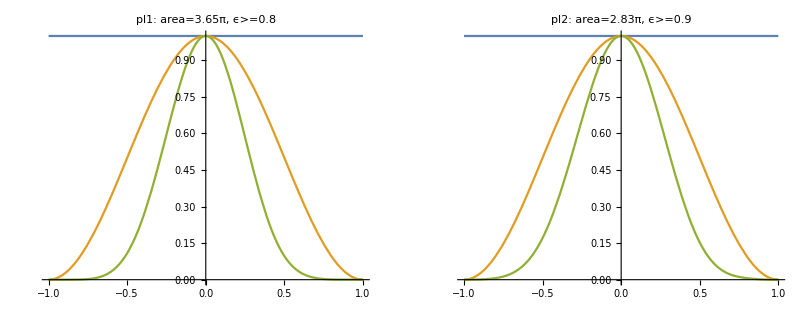

NB4; p=1/2, error=0.001

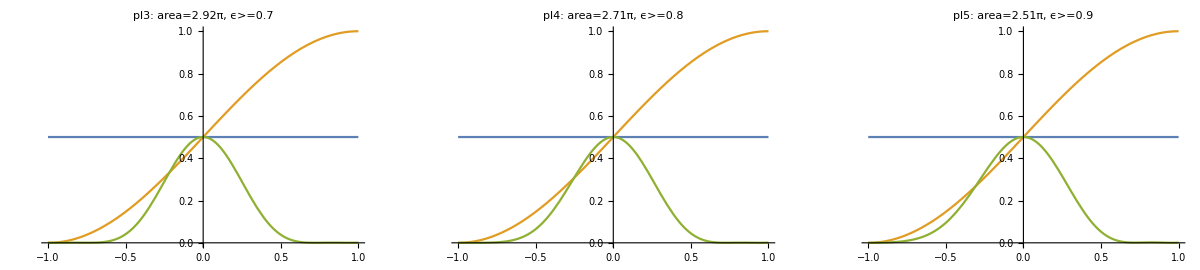

NB4; p=1/3, error=0.001

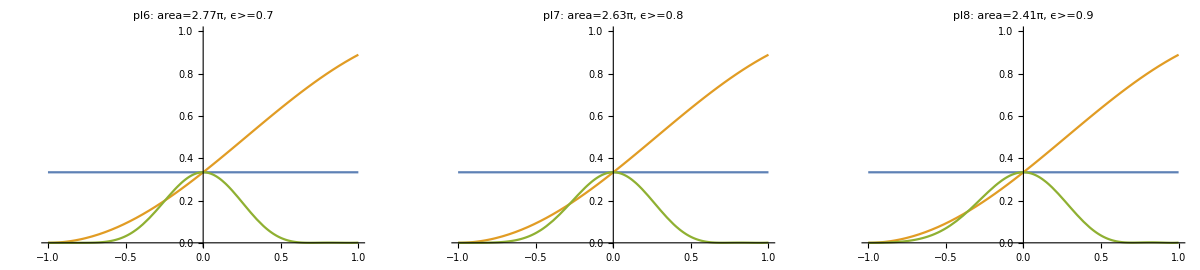

```mathematica
(*N=4*)
sequence=U[Δ4,Ω4].U[Δ3,Ω3].U[Δ2,Ω2].U[Δ1,Ω1];
plt[p_,rule_,label_]:=plot[p,err,sequence,rule,0,label, totalArea[rule,False]]

pl1=plt[1,{Δ1->2.2035,Δ2->-0.8032,Δ3->-1.0268,Δ4->0.7482,Ω1->1.1043,Ω2->1.1715,Ω3->0.9224,Ω4->0.4562},"pl1"];
pl2=plt[1,{Δ1->0.8111,Δ2->0.833,Δ3->-0.483,Δ4->0.6891,Ω1->1.4405,Ω2->0.0831,Ω3->0.4719,Ω4->0.8346},"pl2"];

pl3=plt[0.5,{Δ1->0.4085,Δ2->0.9221,Δ3->-0.2897,Δ4->0.269,Ω1->1.4386,Ω2->0.0799,Ω3->0.4934,Ω4->0.9086},"pl3"];
pl4=plt[0.5,{Δ1->0.3961,Δ2->0.9948,Δ3->-0.3086,Δ4->0.2851,Ω1->1.2834,Ω2->0.1865,Ω3->0.3206,Ω4->0.9236},"pl4"];
pl5=plt[0.5,{Δ1->0.2692,Δ2->-0.2223,Δ3->0.984,Δ4->0.4027,Ω1->0.7741,Ω2->0.3511,Ω3->0.2439,Ω4->1.1427},"pl5"];

pl6=plt[1/3,{Δ1->0.3013,Δ2->0.9794,Δ3->-0.2409,Δ4->0.215,Ω1->1.3319,Ω2->0.1334,Ω3->0.3758,Ω4->0.9297},"pl6"];
pl7=plt[1/3,{Δ1->0.2274,Δ2->-0.3279,Δ3->1.0935,Δ4->0.3019,Ω1->0.9463,Ω2->0.236,Ω3->0.2313,Ω4->1.2141},"pl7"];
pl8=plt[1/3,{Δ1->0.3382,Δ2->0.9661,Δ3->-0.1298,Δ4->0.2026,Ω1->1.0922,Ω2->0.2119,Ω3->0.5625,Ω4->0.5443},"pl8"];

GGrid[Text[Style["NB4; p=1"<>error,FontSize->20]],{{pl1,pl2,Null,Null}},ImageSize->Full]
GGrid[Text[Style["NB4; p=1/2"<>error,FontSize->20]],{{pl3,pl4,pl5,Null}},ImageSize->Full]
GGrid[Text[Style["NB4; p=1/3"<>error,FontSize->20]],{{pl6,pl7,pl8,Null}},ImageSize->Full]
```

NB5; p=1, error=0.001

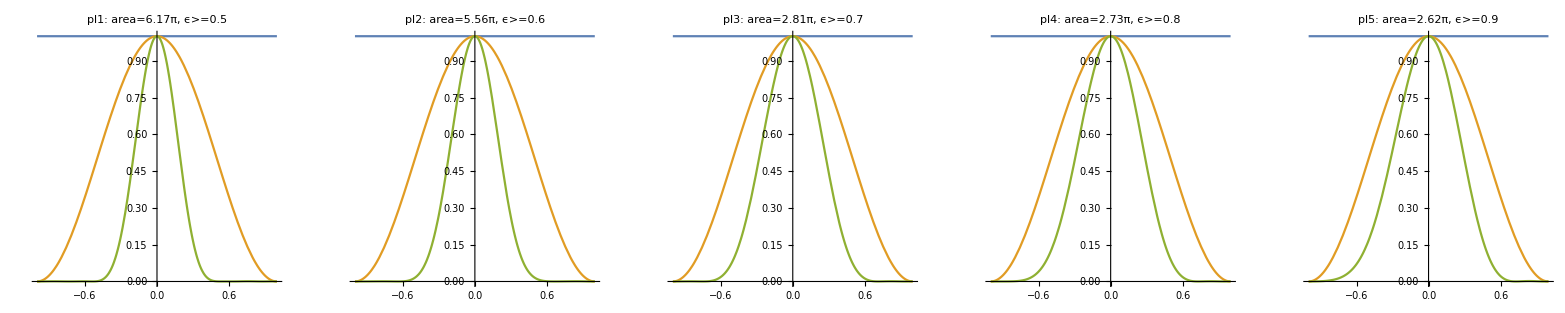

NB5; p=1/2, error=0.001

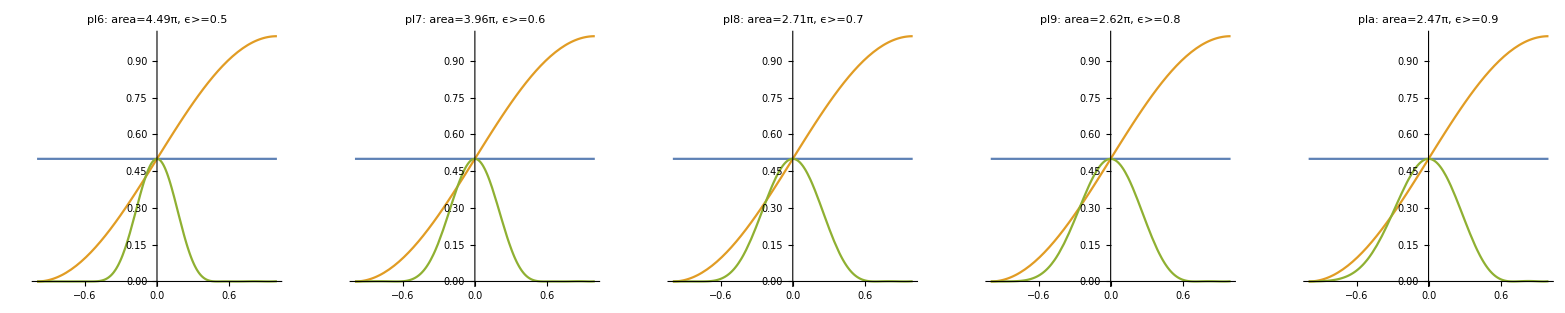

NB5; p=1/3, error=0.001

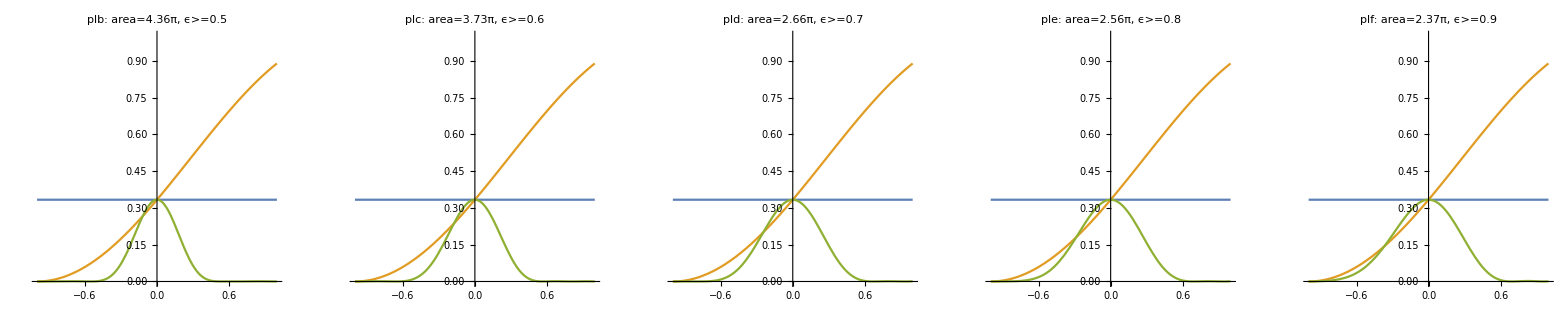

```mathematica
(*N=5*)
sequence=U[Δ1,Ω1].U[Δ2,Ω2].U[Δ3,Ω3].U[Δ2,Ω2].U[Δ1,Ω1];
plt[p_,rule_,label_]:=plot[p,err,sequence,rule,0,label, totalArea[rule,True]]

pl1=plt[1.0,{Δ1->1.5004,Δ2->-1.0657,Δ3->1.7593,Ω1->2.0445,Ω2->0.5622,Ω3->0.9555},"pl1"];
pl2=plt[1.0,{Δ1->1.4899,Δ2->2.3905,Δ3->-0.7226,Ω1->1.6773,Ω2->0.8062,Ω3->0.5937},"pl2"];
pl3=plt[1.0,{Δ1->0.6578,Δ2->-0.1802,Δ3->1.1224,Ω1->0.4716,Ω2->0.4156,Ω3->1.0320},"pl3"];
pl4=plt[1.0,{Δ1->0.6421,Δ2->-0.1476,Δ3->1.1452,Ω1->0.4552,Ω2->0.4265,Ω3->0.9631},"pl4"];
pl5=plt[1.0,{Δ1->0.5873,Δ2->-0.0553,Δ3->1.1056,Ω1->0.4183,Ω2->0.4789,Ω3->0.8210},"pl5"];

pl6=plt[0.5,{Δ1->-0.687,Δ2->1.2322,Δ3->0.1661,Ω1->0.476,Ω2->1.0325,Ω3->1.4768},"pl6"];
pl7=plt[0.5,{Δ1->-0.7473,Δ2->-0.267,Δ3->1.5397,Ω1->0.4076,Ω2->1.1788,Ω3->0.7888},"pl7"];
pl8=plt[0.5,{Δ1->-0.4298,Δ2->0.8254,Δ3->0.3229,Ω1->0.4354,Ω2->0.4701,Ω3->0.9005},"pl8"];
pl9=plt[0.5,{Δ1->-0.3958,Δ2->0.8269,Δ3->0.3617,Ω1->0.4311,Ω2->0.4474,Ω3->0.8665},"pl9"];
pla=plt[0.5,{Δ1->0.7223,Δ2->0.1146,Δ3->0.9641,Ω1->0.4181,Ω2->0.3879,Ω3->0.8601},"pla"];

plb=plt[1/3,{Δ1->0.7897,Δ2->-0.5264,Δ3->1.5358,Ω1->0.4304,Ω2->1.308,Ω3->0.881},"plb"];
plc=plt[1/3,{Δ1->-0.6308,Δ2->1.5006,Δ3->0.3984,Ω1->0.5195,Ω2->0.9549,Ω3->0.7806},"plc"];
pld=plt[1/3,{Δ1->0.7204,Δ2->-0.6364,Δ3->-0.4189,Ω1->0.4562,Ω2->0.7956,Ω3->0.1528},"pld"];
ple=plt[1/3,{Δ1->0.8171,Δ2->0.0504,Δ3->1.0762,Ω1->0.4044,Ω2->0.305,Ω3->1.1408},"ple"];
plf=plt[1/3,{Δ1->0.7545,Δ2->0.1885,Δ3->0.8491,Ω1->0.4285,Ω2->0.3966,Ω3->0.717},"plf"];

GGrid[Text[Style["NB5; p=1"<>error,FontSize->20]],{{pl1,pl2,pl3,pl4,pl5}},ImageSize->Full]
GGrid[Text[Style["NB5; p=1/2"<>error,FontSize->20]],{{pl6,pl7,pl8,pl9,pla}},ImageSize->Full]
GGrid[Text[Style["NB5; p=1/3"<>error,FontSize->20]],{{plb,plc,pld,ple,plf}},ImageSize->Full]
```